# Числено диференциране

## Параметрите a и b са съответно предпоследната и последната цифра от факултетния номер

1. Да се състави таблица за функцията
 g(y) = (y^3 + (b+1)y-a)/(y+2),     y ∈ [2, 4]
 като дадения интервал се раздели на 5 подинтервала.
2. Да се намерят първите производни g' във всички възли.
2. Да се намерят първите производни g'' във всички възли.

## Генериране на данни

```mathematica
a = 2.; b = 4.;
n = 5;
h = (b - a)/n;
```

```mathematica
xt = Table[a + i *h, {i, 0,n}]
```

{2.,2.4,2.8,3.2,3.6,4.}

```mathematica
f[x_] := (x^3 + 8x - 6)/(x + 2)
yt = f[xt]
```

{4.5,6.14182,7.99,10.0708,12.4029,15.}

```mathematica
h = 0.4
```

0.4

```mathematica
n = Length[xt]
```

6

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{4.3625,4.91119,5.51607,6.16154}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{4.3625,4.91119,5.51607,6.16154,6.82418}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{3.84659,4.3625,4.91119,5.51607,6.16154,6.82418}

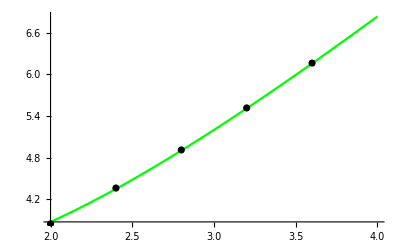

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{1.28977,1.45367,1.57074,1.65659}

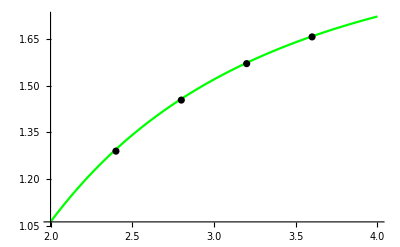

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfypp, grypp2]
```